```mathematica
pts={{60.0010,0.1465},{60.0510,0.1505},{60.1010,0.1625},{60.1510,0.2000},{60.2010,0.2260},{60.2520,0.2755}};
```

```mathematica
fitted=NonlinearModelFit[pts, a t^2+b t + c, {a,b,c}, t]
```

FittedModel[7158.69-238.634 t+1.98874 t^2]

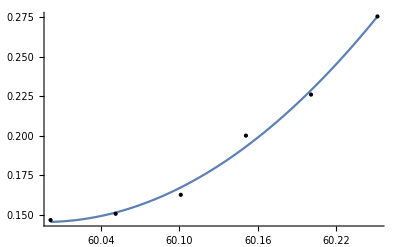

```mathematica
Plot[fitted[t], {t,pts⟦1⟧⟦1⟧,pts⟦Length[pts]⟧⟦1⟧}, Epilog->Table[Point[pts⟦i⟧],{i,1,Length[pts]}]]
```

```mathematica
vel={{0.0260,0.0800},{0.0760,0.2400},{0.1260,0.7500},{0.1760,0.5200},{0.2265,0.9706}};
```

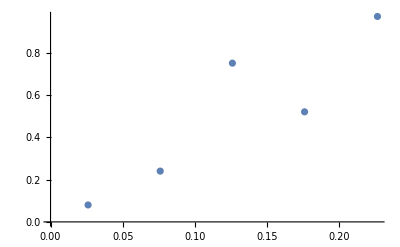

```mathematica
ListPlot[vel]
```

```mathematica
velFitted=LinearModelFit[vel,t,t]
```

FittedModel[-0.00679113+4.11508 t]